```mathematica
Задание 0.
```

```mathematica
f[x_,y_]:=x*y*Log[x^2+y^2]
```

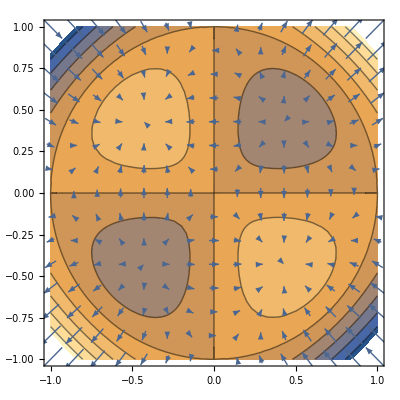

-Graphics3D-

```mathematica
h1=ContourPlot[f[x,y],{x,-1,1},{y,-1,1}];
g1=Grad[f[x,y],{x,y}];
h2=VectorPlot[g1,{x,-1,1},{y,-1,1}];
Show[h1,h2]
Plot3D[f[x,y],{x,-1,1},{y,-1,1}]
```

```mathematica
FindMinimum[f[x,y],{x,-0.5},{y,-0.5}]
```

{-0.18394,{x→-0.428882,y→-0.428882}}

```mathematica
Задание 1.
```

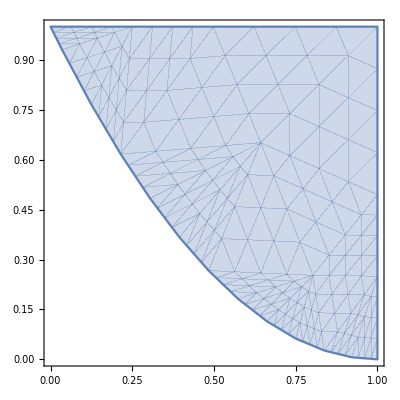

-Graphics3D-

```mathematica
f2a[x_,y_]:=x^2+x+2y;
d2a=ImplicitRegion[x≤1&&y≤1&&y≥ (x-1)^2, {x,y}];
RegionPlot[d2a]
Plot3D[f2a[x,y],{x,0,1},{y,0,1}]
```

```mathematica
Maximize[{f2a[x,y],{x,y}∈d2a},{x,y}]
Minimize[{f2a[x,y],{x,y}∈d2a},{x,y}]
```

{4,{x→1,y→1}}

{5/4,{x→1/2,y→1/4}}

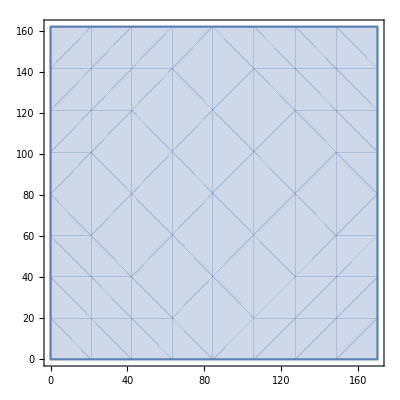

```mathematica
f2b[x_,y_]:=(x+y)*ⅇ^(-(x+2y));
d2b=ImplicitRegion[x>0&&y>0, {x,y}];
RegionPlot[d2b]
```

```mathematica
Plot3D[f2b[x,y],{x,0,10},{y,0,30}]
```

-Graphics3D-

```mathematica
Maximize[{f2b[x,y],{x,y}∈d2b},{x,y}] //N
Minimize[{f2b[x,y],{x,y}∈d2b},{x,y}] //N
```

{1.42802×10^-15,{x→6.43887,y→15.414}}

{0.,{x→93143.4,y→100608.}}

```mathematica
Задание 2.
```

```mathematica
f3a[x_,y_]:=ⅇ^(y^2+2x+1);
f3ax[x_,y_]:=Evaluate[D[f3a[x,y], x]];
f3ay[x_,y_]:=Evaluate[D[f3a[x,y], y]];
plosk3a[xx_,yy_]:=f3ax[1,1]*(xx-1)+f3ay[1,1]*(yy-1)+ f3a[1,1];
Plot3D[{ f3a[x,y],plosk3a[x,y]},{x,0,2},{y,0,2}]
```

-Graphics3D-

```mathematica
Series[f3a[x,y],{x,1,4},{y,1,4}]
```

(ⅇ^4+2 ⅇ^4 (y-1)+3 ⅇ^4 (y-1)^2+10/3 ⅇ^4 (y-1)^3+19/6 ⅇ^4 (y-1)^4+O[y-1]^5)+(2 ⅇ^4+4 ⅇ^4 (y-1)+6 ⅇ^4 (y-1)^2+20/3 ⅇ^4 (y-1)^3+19/3 ⅇ^4 (y-1)^4+O[y-1]^5) (x-1)+(2 ⅇ^4+4 ⅇ^4 (y-1)+6 ⅇ^4 (y-1)^2+20/3 ⅇ^4 (y-1)^3+19/3 ⅇ^4 (y-1)^4+O[y-1]^5) (x-1)^2+((4 ⅇ^4)/3+8/3 ⅇ^4 (y-1)+4 ⅇ^4 (y-1)^2+40/9 ⅇ^4 (y-1)^3+38/9 ⅇ^4 (y-1)^4+O[y-1]^5) (x-1)^3+((2 ⅇ^4)/3+4/3 ⅇ^4 (y-1)+2 ⅇ^4 (y-1)^2+20/9 ⅇ^4 (y-1)^3+19/9 ⅇ^4 (y-1)^4+O[y-1]^5) (x-1)^4+O[x-1]^5

```mathematica
f3b[x_,y_,z_]:=x^2+y^2-4 z^2;
f3bx[x_,y_,z_]:=Evaluate[D[f3b[x,y,z], x]];
f3by[x_,y_,z_]:=Evaluate[D[f3b[x,y,z], y]];
f3bz[x_,y_,z_]:=Evaluate[D[f3b[x,y,z], z]];

ContourPlot3D[{x^2+y^2-4 z^2==1,
f3bx[2,1,1]*(x-2)+f3by[2,1,1]*(y-1)+ f3bz[2,1,1]*(z-1)==0},
 {x, 1, 3}, {y,0,2},{z,0,2}]
```

-Graphics3D-

```mathematica
Задание 3.
```

-Graphics3D-

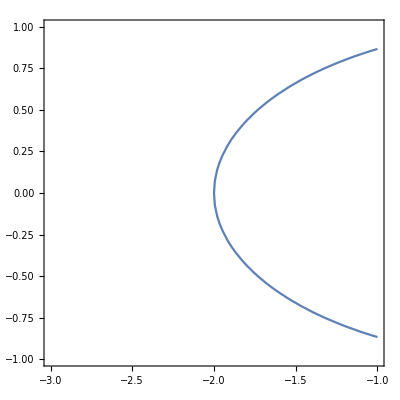

```mathematica
f4[x_,y_]:=x^2+y^2;
Plot3D[f4[x,y], {x, -3,-1},{y,-1,1}]
ContourPlot[x^2/4+y^2==1,{x,-3,-1},{y,-1,1}]
```

```mathematica
Maximize[{f4[x,y],x^2/4+y^2==1}, {x,y}]
```

{4,{x→-2,y→0}}